```mathematica
h=Table[If[i==j,2+500/10201 Sin[π j/101],0],{i,100},{j,100}];
```

```mathematica
k=Table[If[i==j+1,-1,0],{i,100},{j,100}];
```

```mathematica
m=Table[If[i==j-1,-1,0],{i,100},{j,100}];
```

```mathematica
p=Table[h[[i,j]]+k[[i,j]]+m[[i,j]],{i,100},{j,100}];
```

```mathematica
eig=Eigenvalues[N[p]];
```

```mathematica
En=10201*eig;
```

```mathematica
TakeSmallest[En,3]
```

{304.66,304.8,476.163}

```mathematica
eve=Eigenvectors[N[p]];
```

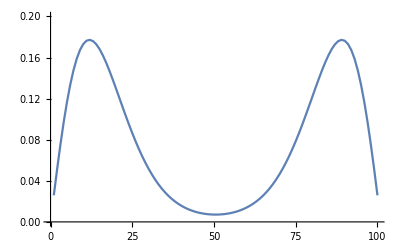

```mathematica
ListLinePlot[eve[[100]],PlotRange->{0,.2}]
```

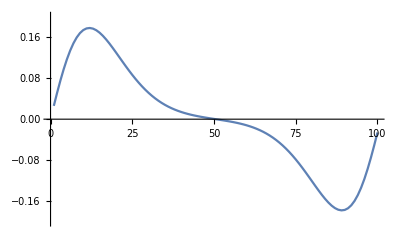

```mathematica
ListLinePlot[eve[[99]],PlotRange->{-.2,.2}]
```

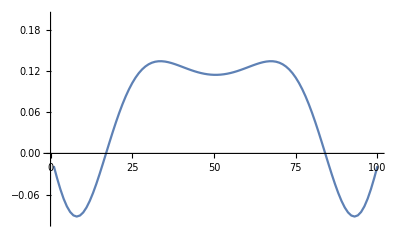

```mathematica
ListLinePlot[eve[[98]],PlotRange->{-.1,.2}]
```